# Kerr quasinormal modes and residues

## The question

A more strongly damped mode decays faster in time, but its residue can be larger. Their competition determines when the overtone sum converges. At fixed angular labels, the pole contribution to the Green function is

G_sℓm^poles(x,x')==-i/(2π) e^(im(ϕ-ϕ'))∑_n e^(-i ω_sℓmn(t-t')) ℛ_sℓmn.

We compute the quasinormal frequencies and the complete residues, then compare their spatial dependence with the WKB prediction. The two families have growth rates Γ_pr and Γ_ob; under the large-damping assumptions of the paper, both sums converge absolutely for t-t'>max(Γ_pr,Γ_ob).

The examples use a/M = 0.7, s = −2 and m = 2. The notebook gives the algorithm, generates the data and shows a few checks. The final paper figures are plotted in Python. The saved figures show the completed calculation. Data are read from and written to data/.

## 01 Conventions and units

We use a/M==0.7. The numerical calculation sets 2M==1, so the parameter in the code is a==7/20:

M==1/2,    a==7/10 M==7/20.

Frequencies and radii in the solver are 2Mω and r/(2M). Figures and tables report Mω, the damping x_n==-M ω_(I,n) and r/M. With time dependence e^-iωt, damped modes have ω_I<0.

Residues retain the 2M==1 normalization. With the source convention used here, converting them to the paper's M==1 variables multiplies them by four. This factor cancels from growth rates, ratios and fitted powers; it remains in the magnitude plots and the fitted constant c.

A source–observer configuration is passed as {r/M,r'/M,θ,θ'}, with the observer first. The corresponding functions convert the radii to solver units.

For a new calculation leave compute = True and evaluate all cells. Allow roughly 6–9 hours; the high-overtone maps take most of the time. False reads output/ if it exists, otherwise the supplied data/. Completed poles are reused when restarting. Change runDirectory for a fresh run.

```mathematica
Clear[pole, radialSeries];
notebookDirectory = If[$Notebooks, NotebookDirectory[], Directory[]];
compute = True;                 (* False: read the completed calculation. *)
runDirectory = FileNameJoin[{notebookDirectory, "data"}];
workers = Min[4, Max[1, $ProcessorCount - 2]];
dataDirectory = If[compute || DirectoryQ[runDirectory], runDirectory,
  FileNameJoin[{notebookDirectory, "output"}]];
```

Read and write the calculation

```mathematica
readData[file_] := If[FileExistsQ[file],
  If[FileExtension[file] == "json", Import[file, "RawJSON"], Import[file]],
  Print["Required file: ", file]; Abort[]];
saveData[file_, value_] := Module[{folder = DirectoryName[file], temporary = file <> ".tmp", format},
  If[!DirectoryQ[folder], CreateDirectory[folder, CreateIntermediateDirectories -> True]];
  format = If[FileExtension[file] == "json", "RawJSON", "WXF"];
  If[Export[temporary, value, format] === $Failed, Print["Could not write ", file]; Abort[]];
  RenameFile[temporary, file, OverwriteTarget -> True]; value];
SetAttributes[obtain, HoldRest];
obtain[name_, calculation_] := Module[{file = FileNameJoin[{dataDirectory, name}], value},
  If[FileExistsQ[file], Return[readData[file]]];
  If[!compute, Print["Required file: ", file]; Abort[]];
  value = calculation;
  If[value === $Failed || value === $Aborted || FailureQ[value], Print["Calculation failed: ", name]; Abort[]];
  saveData[file, value]];
If[compute,
  runInfo = <|"version" -> "Kerr-QNM-final-20261115-1", "a_over_M" -> 7/10,
    "s" -> -2, "m" -> 2, "high_pairs" -> {{8000,16000},{4000,6000}}|>;
  infoFile = FileNameJoin[{dataDirectory, "calculation.wxf"}];
  If[FileExistsQ[infoFile] && readData[infoFile] =!= runInfo,
    Print["Use a new output folder for this calculation."]; Abort[]];
  If[!FileExistsQ[infoFile], saveData[infoFile, runInfo]]];
```

## Parameters

In units 2M==1, the horizons and tortoise coordinate are

Δ  |  ==r^2-r+a^2,    r_±==(1±√(1-4 a^2))/2, 
 r_*  |  ==r+(r_+log(r-r_+)-r_-log(r-r_-))/(r_+-r_-).

The logarithms are real for r>r_+. The code uses horizonGap for r_+-r_-.

```mathematica
a = 7/20; s = -2; m = 2;
rPlus = (1 + Sqrt[1 - 4 a^2])/2;
rMinus = 1 - rPlus;
horizonGap = rPlus - rMinus;
delta[r_] := r^2 - r + a^2;
rStar[r_] := r + (rPlus Log[r - rPlus] - rMinus Log[r - rMinus])/horizonGap;
N[2 {rPlus, rMinus}]       (* r+/M and r-/M *)
```

{1.71414,0.285857}

## Figures and tables

Shared plot and table formatting

```mathematica
familyColor = <|"prolate" -> RGBColor["#0071E3"], "oblate" -> RGBColor["#F56300"]|>;
sigmaName = <|"prolate" -> "pr", "oblate" -> "ob"|>;
SetOptions[#, Frame -> True, Axes -> False, ImageSize -> 360,
    LabelStyle -> {FontFamily -> "Times", FontSize -> 13, GrayLevel[0.1]}] & /@
  {Plot, ListPlot, ListLinePlot, ListLogPlot, ListLogLinearPlot, ContourPlot, RegionPlot, ArrayPlot, ListDensityPlot};
showTable[header_, rows_] := Grid[Prepend[rows, Style[#, Bold] & /@ header], Frame -> All,
   FrameStyle -> GrayLevel[0.75], Spacings -> {1.5, 0.6}];
```

## 02 Seeds and numerical settings

We start each pole search from an approximate frequency and angular eigenvalue, then refine both together. Throughout the calculation, frequencies and radii are in units 2M==1.

## Starting frequencies

The damping is nearly equally spaced along each family. We obtain initial guesses by fitting previously computed frequencies with

Re ω_n≃c_0+c_1/n+c_2/n^2,    -Im ω_n≃d n+d_0+d_1/n+d_2/n^2.

The fitted coefficients are listed below. Here n labels the poles within each family according to the fitted sequence.

```mathematica
(* {{c0, c1, c2}, {d, d0, d1, d2}} *)
law = <|
   "oblate" -> {{0.8167446027, -0.01493195864, 3.05350224},
       {0.41661801805, -0.41654023288, -0.046873806066, 9.4126248334}},
   "prolate" -> {{-0.2299254974, -1.025945752, 26.73327452},
       {0.510727127, -3.9682938417, 1.9413673676, 26.686669516}}|>;
seedOmega[family_, n_] := Module[{c, d},
   {c, d} = law[family];
   c . {1, 1/n, 1/n^2} - I d . {n, 1, 1/n, 1/n^2}];
```

The oblate fit is close to the horizon expression

ω_n≃m Ω_H-i κ_+(n-1),    Ω_H==a/(r_+),    κ_+==(r_+-r_-)/(2 r_+).

Here Ω_H and κ₊ are the angular velocity and surface
gravity of the outer horizon.

```mathematica
Module[{c, d, kappaPlus = horizonGap/(2 rPlus)},
 {c, d} = law["oblate"];
 NumberForm[showTable[{"oblate law", "fitted", "horizon"},
   {{"c0", c[[1]], N[m a/rPlus]}, {"d", d[[1]], N[kappaPlus]}, {"d0", d[[2]], N[-kappaPlus]}}], 10]]
```

oblate law | fitted | horizon
c0 | 0.8167446027 | 0.8167347347
d | 0.4166180181 | 0.4166180466
d0 | -0.4165402329 | -0.4166180466

The fitted spacing agrees with κ₊ to seven digits.
Both fits can be compared with the known large-damping spectra: Keshet–Ben-Meir for oblate modes and Keshet–Hod for prolate modes. You can find all the references in our paper.

## Starting angular eigenvalues

The angular solve follows the eigenvalue nearest to its starting guess. We use the large-damping behavior A_ob∼-(aω)^2 and A_pr∼iaω, with the following corrections. The prolate coefficients were fitted to the same poles as the frequencies.

A_ob≃-(aω)^2-2aω+3,    A_pr≃α_1 ω+α_0+(α_-1)/ω,  α_1≃ia.

```mathematica
seedA["oblate", w_] := -(a w)^2 - 2 a w + 3;
seedA["prolate", w_] := (0.00064 + 0.34881 I) w + 9.86382 + 0.31351 I + (30.17167 + 27.03122 I)/w;
```

## 03 The angular problem

At each trial frequency we need the angular eigenvalue A(ω) for the radial equation and the eigenfunction S(θ) for the residue. We expand S in spin-weighted spherical harmonics. This basis already enforces regularity at θ==0,π.

## The angular matrix

With s==-2, m==2 and S==∑_(ℓ==2)^ℓ_max v_ℓ Y_ℓ, the angular equation becomes

M(ω) v==A v,    M==D+2saω C-(aω)^2 C^2.

D contains the spherical eigenvalues. C represents multiplication by cosθ and couples only neighboring harmonics:

D_ℓℓ  |  ==(ℓ-s)(ℓ+s+1),    C_ℓℓ==-ms/(ℓ(ℓ+1)), 
 C_(ℓ-1,ℓ)  |  ==C_(ℓ,ℓ-1)==(√((ℓ^2-m^2)(ℓ^2-s^2)))/(ℓ √(4 ℓ^2-1)).

The basis ends at ℓ_max== basisSize[w]. Squaring the truncated C differs from projecting cos^2 θ only in the last diagonal entry; extending the basis made this difference negligible in the tested eigenvalues and projectors.

```mathematica
(* Rows correspond to l = 2, ..., lmax. *)
angularBlocks[lmax_, digits_] := Module[{ell = Range[2, lmax], coupling, cosine},
   coupling = Table[Sqrt[(l^2 - m^2) (l^2 - s^2)]/(l Sqrt[4 l^2 - 1]), {l, 3, lmax}];
   cosine = SparseArray[{Band[{1, 1}] -> -m s/(ell (ell + 1)),
       Band[{1, 2}] -> coupling, Band[{2, 1}] -> coupling}];
   N[{SparseArray[Band[{1, 1}] -> (ell - s) (ell + s + 1)], cosine, cosine . cosine}, digits]];
```

### Angular resolution

The angular cutoff and working precision increase with frequency. We truncate the angular expansion at ℓ_max and use   p_ang  decimal digits of working precision. We use the following empirical prescriptions, checked by increasing the cutoff and working precision. We use

ℓ_max==⌈|aω|+28|aω|^(1/3)+20⌉,    p_ang==max(150,⌈0.45|aω|⌉+70).

Here p is the number of working digits. The extra margin allows for truncation and cancellation.

```mathematica
basisSize[w_] := Ceiling[a Abs[w] + 28 (a Abs[w])^(1/3) + 20];
angularDigits[w_] := Max[150, Ceiling[0.45 a Abs[w]] + 70];
```

## Following one eigenvalue

Eigensystem finds the angular eigenpair nearest to the starting guess. We check its residual before using the result.

For a simple eigenvalue, the frequency derivative follows from the symmetry of the angular matrix:

dA/dω==(v^T M' v)/(v^T v),    M'==2sa C-2 a^2 ω C^2.

These products use the transpose without complex conjugation.

```mathematica
angularMode[omega_, guessA_, lmax_, digits_] :=
 Module[{d, c, c2, w = SetPrecision[omega, digits], matrix, values, vectors, A, v},
  {d, c, c2} = angularBlocks[lmax, digits];
  matrix = d + 2 s a w c - a^2 w^2 c2;
  {values, vectors} = Eigensystem[matrix, -1,
    Method -> {"Arnoldi", "Shift" -> SetPrecision[guessA, digits],
      "Tolerance" -> 10^(20 - digits), "MaxIterations" -> 1000,
      "StartingVector" -> ConstantArray[1, lmax - 1]}];
  A = First[values];
  v = First[vectors]; v = v/Norm[v];
  <|"A" -> A, "v" -> v,
    "dA" -> v . (2 s a c - 2 a^2 w c2) . v/(v . v),
    "norm" -> v . v,
    "converged" -> TrueQ[Norm[matrix . v - A v] < 10^(30 - digits) Abs[A]]|>];
```

The result contains A, its eigenvector, its frequency derivative and the bilinear norm. We require the eigenpair residual check to pass. Here are the two families at the starting frequencies for n = 500:

```mathematica
exampleModes = obtain["examples/angular.wxf", Table[With[{w = seedOmega[family, 500]},
    Join[<|"family" -> family, "omega" -> w|>,
     angularMode[w, seedA[family, w], basisSize[w], angularDigits[w]]]],
   {family, {"prolate", "oblate"}}]];
showTable[{"family","aω","A","dA/d(Mω)"},Table[{mode["family"],N[a mode["omega"],6],N[mode["A"],10],N[2 mode["dA"],6]},{mode,exampleModes}]]
```

family | aω | A | dA/d(Mω)
prolate | -0.0811547-87.9897 ⅈ | 97.30031723+0.1046827 ⅈ | 0.00151+0.699564 ⅈ
oblate | 0.285854-72.7623 ⅈ | 5296.711205+187.13692 ⅈ | -1.816+101.859 ⅈ

The prolate derivative is close to ia, and the oblate derivative to -2 a^2 ω-2a, as expected from the starting forms. The table shows dA/d(Mω), twice the derivative in the internal units.

## The angular wave and projector

For s = -2 and m = 2, the normalized polar parts of the spin-weighted spherical harmonics are

Y_ℓ(θ)=√((2ℓ+1)/2)((1+x)/2)^2 P_(ℓ-2)^(0,4)(x),   x=cosθ.

We evaluate the Jacobi polynomials by their standard three-term recurrence, starting from the first two polynomials. The eigenvector supplies the expansion coefficients:

S(θ)=∑_(ℓ=2)^ℓ_max v_ℓ Y_ℓ(θ).

angularProfile divides the wave by the square root of its bilinear norm, without complex conjugation. The product of two profiles gives the projector. Use exact or high-precision angles.

```mathematica
angularWave[v_, x_List] := Module[{previous = ConstantArray[1, Length[x]], current = 3 x - 2,
    next, sum},
   sum = v[[1]] Sqrt[5/2] previous + v[[2]] Sqrt[7/2] current;
   Do[
    next = ((2 j + 3) ((2 j + 2) (2 j + 4) x - 16) current - 2 (j - 1) (j + 3) (2 j + 4) previous)/
      (2 j (j + 4) (2 j + 2));
    sum += v[[j + 1]] Sqrt[(2 j + 5)/2] next;
    {previous, current} = {current, next},
    {j, 2, Length[v] - 1}];
   ((1 + x)/2)^2 sum];

(* Use the eigenvector working precision for the angular sum. *)
angularProfile[p_, angles_] :=
   angularWave[p["v"], N[Cos[angles], Precision[p["v"]]]]/Sqrt[p["norm"]];
```

The harmonic coefficients and angular profiles of the two examples are:

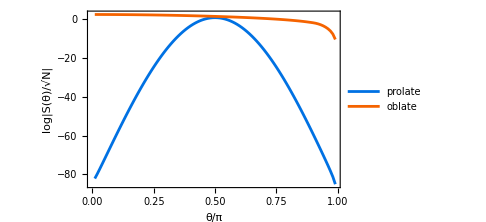

```mathematica
exampleAngles=Pi Range[99]/100;

ListLinePlot[Table[Transpose[{N[exampleAngles/Pi],N[Log[Abs[angularProfile[mode,exampleAngles]]]]}],{mode,exampleModes}],Frame->True,PlotRange->All,PlotStyle->familyColor/@{"prolate","oblate"},PlotLegends->{"prolate","oblate"},FrameLabel->{"θ/π","log|S(θ)/√N|"}]
```

The prolate angular profile is concentrated near the equator and strongly suppressed near the poles. The oblate profile is broader.

## 04 The radial solutions

At each trial frequency, we evaluate the horizon-ingoing solution R_IN and match it to R_∞^in and R_∞^out. This gives the amplitudes B_in and B_out needed to find the pole. Once the pole is known, we evaluate the radial factor R_IN/B_out at the source and observer.

## The horizon solution

Factoring out the exponential and horizon powers reduces the radial equation to the confluent Heun equation. In units 2M==1,

R_IN(r)  |  ==P(r)H(x),    P(r)==e^-iωr(r-r_+)^(-s-i η_+)(r-r_-)^(-s+i η_-), 
 x  |  ==(r_+-r)/(r_+-r_-),    η_±==(ω r_±-am)/(r_+-r_-).

We use the solution regular at x==0, with H(0)==1. Its equation and parameters are

H''+(γ/x+δ/(x-1)+ϵ)H'+(αx-q_H)/(x(x-1))H==0,

ϵ  |  ==2iω(r_+-r_-),  |  α  |  ==(1-2s)ϵ, 
 γ  |  ==1-s-2i η_+,  |  δ  |  ==1-s+2i η_-, 
 q_H  |  ==λ+2s+2i(1-2s)r_+ω,  |  λ  |  ==A+a^2 ω^2-2amω.

This is Mathematica's HeunC[qH, alphaH, gammaH, deltaH, epsilon, x]. For the matching we also need the radial derivative. HeunCPrime differentiates with respect to x, so the chain rule gives

(d R_IN)/dr==P[(-iω+(-s-i η_+)/(r-r_+)+(-s+i η_-)/(r-r_-))H-H'/(r_+-r_-)].

RIN returns the pair {R_IN,d R_IN/dr}. Passing False as its last argument returns only the value, avoiding an unnecessary derivative when plotting a profile. The caller supplies the working precision because HeunC uses the lowest precision among its arguments.

```mathematica
RIN[r_, w_, A_, withDerivative_ : True] := Module[{lambda, etaPlus, etaMinus, epsilon, alphaH, gammaH, deltaH, qH, x,
    H, dH, prefactor, slope},
   lambda = A + a^2 w^2 - 2 a m w;
   etaPlus = (w rPlus - a m)/horizonGap; etaMinus = (w rMinus - a m)/horizonGap;
   epsilon = 2 I horizonGap w; alphaH = (1 - 2 s) epsilon;
   gammaH = 1 - s - 2 I etaPlus; deltaH = 1 - s + 2 I etaMinus;
   qH = lambda + 2 s + 2 I (1 - 2 s) rPlus w;
   x = (rPlus - r)/horizonGap;
   H = HeunC[qH, alphaH, gammaH, deltaH, epsilon, x];
   prefactor = Exp[-I w r] (r - rPlus)^(-s - I etaPlus) (r - rMinus)^(-s + I etaMinus);
   If[! withDerivative, Return[prefactor H]];
   dH = -HeunCPrime[qH, alphaH, gammaH, deltaH, epsilon, x]/horizonGap;
   slope = (-s - I etaPlus)/(r - rPlus) + (-s + I etaMinus)/(r - rMinus) - I w;
   prefactor {H, H slope + dH}];
```

## The two solutions at infinity

We use the incoming and outgoing asymptotic expansions, with the first coefficient set to one:

R_∞^in(r)  |  ≃r^-1 e^(-iω r_*)∑_(k==0)^k_max d_k^in r^-k, 
 R_∞^out(r)  |  ≃r^3 e^(iω r_*)∑_(k==0)^k_max d_k^out r^-k,    d_0^in==d_0^out==1.

Substitution into the radial Teukolsky equation determines the coefficients order by order. The code derives the relation once for each direction: sign = -1 for incoming and +1 for outgoing.

```mathematica
Clear[recurrenceRow];

(* Substitute a generic term of the expansion into the radial equation. *)
recurrenceRow[sign_] := recurrenceRow[sign] = Module[
  {r, k, w, lambda, R, K, equation, coefficients},
  R = r^(1 + 2 sign - k) Exp[sign I w rStar[r]];
  K = (r^2 + a^2) w - a m;
  equation = delta[r] D[R, {r, 2}] + (s + 1) D[delta[r], r] D[R, r]
    + ((K^2 - 2 I s (r - 1/2) K)/delta[r] + 4 I s w r - lambda) R;
  coefficients = CoefficientList[FullSimplify[r^2 delta[r] equation/R], r];
  Function[{order, omega, separation},
    coefficients /. {k -> order, w -> omega, lambda -> separation}]];

(* Fix d0 = 1 and determine the remaining coefficients in order. *)
seriesCoefficients[w_, A_, sign_, terms_] := Module[{rows, d},
  rows = Table[recurrenceRow[sign][k, w, A + a^2 w^2 - 2 a m w], {k, 0, terms}];
  d = Prepend[ConstantArray[0, terms], 1];
  Do[d[[k + 1]] = -Sum[rows[[k - j + 1, 6 - j]] d[[k - j + 1]],
      {j, 1, Min[5, k]}]/rows[[k + 1, 6]], {k, 1, terms}];
  d];
```

RinfIn and RinfOut return the solution and its radial derivative. The same coefficients can be reused at different radii.

```mathematica
Rinf[d_, r_, w_, sign_] := Module[{k = Range[0, Length[d] - 1], series, prefactor, slope},
  series = d/r^k;
  prefactor = r^(1 + 2 sign) Exp[sign I w rStar[r]];
  slope = (1 + 2 sign)/r + sign I w (r^2 + a^2)/delta[r];
  prefactor {Total[series], slope Total[series] - k.series/r}];

RinfIn[d_, r_, w_] := Rinf[d, r, w, -1];
RinfOut[d_, r_, w_] := Rinf[d, r, w, 1];
```

## Matching the amplitudes

The solution and its derivative satisfy the same linear combination,

R_IN==B_in R_∞^in+B_out R_∞^out.

Solving this 2×2 system with W[f,g]==f g'-f' g gives

B_in==W[R_IN,R_∞^out]/W[R_∞^in,R_∞^out],    B_out==W[R_∞^in,R_IN]/W[R_∞^in,R_∞^out].

The weighted Wronskian has an extra factor Δ^(s+1), which cancels from these ratios.

```mathematica
wronskian[{f_, df_}, {g_, dg_}] := f dg - df g;
match[R_, Rin_, Rout_] := {wronskian[R, Rout], wronskian[Rin, R]}/wronskian[Rin, Rout];
amplitudes[r_, w_, A_, terms_] := match[RIN[r, w, A],
   RinfIn[seriesCoefficients[w, A, -1, terms], r, w],
   RinfOut[seriesCoefficients[w, A, 1, terms], r, w]];
```

### Matching point

To extract the two radial amplitudes, we match where the incoming and outgoing exponential factors have equal modulus:

Im[ω r_*(r)]==0,    Im r==sgn(Re ω)max(2,40/Abs[ω]).

This empirical choice of height keeps the matching point away from the horizons and |ωr| large. The sign selects the half-plane; the real part is found from the equal-modulus condition.

```mathematica
matchingRadius[w_] := Module[{height = Sign[Re[w]] Max[2, 40/Abs[w]], x},
   Rationalize[x /. FindRoot[Im[w rStar[x + I height]], {x, -1, -1.1}], 10^-10]
    + I Rationalize[height, 10^-2]];
```

We truncate the asymptotic series before the estimated onset of growing terms, with a maximum order of 512:

k_max==min(512,⌊0.8|2ωr|⌋).

```mathematica
seriesTerms[w_, r_] := Min[512, Floor[0.8 Abs[2 w r]]];
```

At large real radius, the outgoing solution of a damped mode is exponentially larger. Extracting a small incoming amplitude then requires subtracting very large numbers. The condition Im(ω r_*)==0 removes this exponential imbalance, leaving the leading ratio |r|^4. The asymptotic representation also depends on the complex direction, which is fixed by matchingRadius. For the oblate seed n==1000:

```mathematica
Module[{w = seedOmega["oblate", 1000], rm},
  rm = N[matchingRadius[w]];
  showTable[{"r/M", Row[{"log10 leading |", Subsuperscript["R", "∞", "out"], "/",
     Subsuperscript["R", "∞", "in"], "|"}]},
   Table[{NumberForm[2 r, {3, 2}], NumberForm[Log10[Abs[r^4 Exp[2 I w rStar[r]]]], 4]}, {r, {rm, Abs[rm]}}]]]
```

r/M | log10 leading |R_∞^out/R_∞^in|
-2.08+4.00 ⅈ | 1.412
4.51 | 907.2

At the real radius, the outgoing exponential is larger by about nine hundred orders of magnitude. At the complex matching radius, the exponential factors have equal modulus.

## The profile on real radii

At a pole, the radial factor entering the residue is f==R_IN/B_out. Direct Heun evaluation becomes slow at larger radii, so we use the asymptotic series beyond a matching point r_0:

f(r)≃R_∞^out(r)+ρ R_∞^in(r).

The outgoing coefficient is kept equal to one, as at the complex matching point. We determine ρ from the Heun solution and its derivative at r_0, using the same Wronskian match. This accounts numerically for the incoming contribution on the real axis. Stokes behavior motivates this representation; its accuracy here is checked by direct comparison with Heun.

For a deep pole, r_0 lies inside the bounce, where the incoming term dominates. The match then resolves ρ well but cannot independently determine the small outgoing term. Keeping its coefficient equal to one also agrees with the tested Heun profiles outside the bounce, where the outgoing term dominates.

We choose

r_0==max(1.1,220/(|2ω|)),

which imposes r≥2.2M and |2ωr|≥220 before using the series. The first condition avoids the horizon; the second keeps the series in the large-Abs[ωr] regime. Across twelve tested poles with n==100–1000, the largest relative difference from the Heun profile was 4×10^-10. For prolate 204, 500, 1000 and oblate 1200, whose r_0 is inside the bounce, the agreement was 5×10^-11 or better at r/M==2.2, 2.5, 3, 4 and 6.

```mathematica
radialExact[p_, radii_] :=
   Table[RIN[SetPrecision[r, p["digits"]], p["omega"], p["A"], False]/p["Bout"], {r, radii}];

seriesStart[w_] := Max[11/10, 220/Abs[2 w]];

radialSeries[p_, radii_] := Module[{w = p["omega"], A = p["A"], r0, terms, dIn, dOut, rho},
   If[radii === {}, Return[{}]];
   r0 = SetPrecision[seriesStart[w], p["digits"]];
   terms = seriesTerms[w, r0];
   dIn = seriesCoefficients[w, A, -1, terms];
   dOut = seriesCoefficients[w, A, 1, terms];
   rho = First[match[RIN[r0, w, A], RinfIn[dIn, r0, w], RinfOut[dOut, r0, w]]]/p["Bout"];
   Table[First[RinfOut[dOut, r, w]] + rho First[RinfIn[dIn, r, w]],
       {r, SetPrecision[radii, p["digits"]]}]];

(* Preserve the input order even when the radii straddle r0. *)
radialProfile[p_, radii_] := Module[{r0 = seriesStart[p["omega"]], near, far, values},
   near = Select[radii, # < r0 &];
   far = Select[radii, # >= r0 &];
   values = AssociationThread[Join[near, far] -> Join[radialExact[p, near], radialSeries[p, far]]];
   Lookup[values, radii]];
```

radialProfile uses Heun below r_0 and the series above it. It needs only the frequency, angular eigenvalue, B_out and working precision, so it also works with saved pole records.

## 05 The pole and its residue

With unit outgoing normalization for R_UP, the weighted Wronskian is Ŵ==2iω B_in. We find a QNM by setting B_in==0. In practice we use the ratio B_in/B_out, which removes the arbitrary normalization of R_IN.

### Working precision

The radial evaluation uses more working digits as the damping increases:

p_rad==max(150,⌈1.05|Im ω|⌉+40).

```mathematica
radialDigits[w_] := Max[150, Ceiling[1.05 Abs[Im[w]]] + 40];
```

For each pole search, the working precisions, angular cutoff, matching point and series order are set from the starting frequency and kept fixed.

## Finding the QNM frequencies

We find each QNM frequency by solving the vanishing incoming-amplitude condition along the selected angular branch:

β(ω)≡(B_in(ω,A(ω)))/(B_out(ω,A(ω)))=0

Starting from the asymptotic seed, we use Newton's update

δω=-(β(ω))/(β'(ω)),  ω_new=ω+δω.

The same root-finding problem could also be solved with FindRoot. At each trial frequency, we recompute the angular eigenvalue and then the radial amplitudes. The total derivative β'(ω) includes the variation of A(ω); it is estimated with a finite-difference step h=10^-20 and saved as dBeta for the residue.

With the default tolerance, the iteration stops when |δω|<10^-12, with at most twelve iterations. The result is marked converged -> False if this criterion is not met or the final angular solve has not converged. All returned quantities refer to the last evaluated frequency.

```mathematica
pole[family_, n_, tolerance_ : 10^-12] := Module[{seed = seedOmega[family, n], h = 10^-20,
    digits, radius, terms, w, A, angular, dA, Bin, Bout, BinH, BoutH, ratio, dRatio, move,
    converged, steps = 0},
   digits = radialDigits[seed];
   radius = SetPrecision[matchingRadius[seed], digits];
   terms = seriesTerms[seed, radius];
   w = SetPrecision[seed, digits];
   A = seedA[family, seed];
   While[True,
    steps++;
    angular = angularMode[w, A, basisSize[seed], angularDigits[seed]];
    {A, dA} = SetPrecision[{angular["A"], angular["dA"]}, digits];   (* match the Heun working precision *)
    {Bin, Bout} = amplitudes[radius, w, A, terms];
    {BinH, BoutH} = amplitudes[radius, w + h, A + h dA, terms];
    ratio = Bin/Bout;
    dRatio = (BinH/BoutH - ratio)/h;
    move = -ratio/dRatio;
    converged = TrueQ[Abs[move] < tolerance];
    If[converged || steps == 12, Break[]];
    w = SetPrecision[w + move, digits];
    A += dA move];   (* predict A at the next frequency *)
   <|"family" -> family, "n" -> n, "omega" -> w, "A" -> A, "v" -> angular["v"],
    "norm" -> angular["norm"], "Bout" -> Bout, "dBeta" -> dRatio, "digits" -> digits,
    "iterations" -> steps, "lastMove" -> N[Abs[move]],
    "seedShift" -> N[Abs[w - seed]], "converged" -> converged && angular["converged"]|>];
```

## The complete residue

At a simple pole ω_n, the complete residue is

ℛ_n(r,r',θ,θ')=(R_(IN,n)(r_<) R_(UP,n)(r_>))/([(d Ŵ)/dω]_ω_n) (S_n(θ) S_n(θ'))/N_n=1/(2 i ω_n [d/dω(B_in/B_out)]_ω_n) (R_(IN,n)(r))/(B_(out,n)) (R_(IN,n)(r'))/(B_(out,n)) (S_n(θ) S_n(θ'))/N_n.

Here r_<=min(r,r') and r_>=max(r,r'). The second equality uses B_in(ω_n)=0, R_(UP,n)=(R_(IN,n))/(B_(out,n)), and Ŵ=2 i ω B_in, which gives

[(d Ŵ)/dω]_ω_n=2 i ω_n B_(out,n) [d/dω(B_in/B_out)]_ω_n.

The derivative of B_in/B_out is total along the angular eigenvalue A(ω); the pole record stores its value as dBeta. Recalling the radial profile defined above, we write

f_n(r)=(R_(IN,n)(r))/(B_(out,n)),    c_n=1/(2 i ω_n [d/dω(B_in/B_out)]_ω_n),

ℛ_n=c_n f_n(r) f_n(r') (S_n(θ) S_n(θ'))/N_n.

The code evaluates the radial and angular profiles at the observer and source, then multiplies them by c_n. The angular product uses the bilinear normalization, without complex conjugation. Both radial factors are the same function, so their radii need not be sorted.

```mathematica
poleConstant[p_] := 1/(2 I p["omega"] p["dBeta"]);
residue[p_, {r_, rPrime_, theta_, thetaPrime_}] := Module[{f = radialExact[p, {r, rPrime}/2],
    S = angularProfile[p, {theta, thetaPrime}]},
   poleConstant[p] f[[1]] f[[2]] S[[1]] S[[2]]];
```

The input radii are r/M and r'/M; division by two converts them to the internal units. The residue retains the 2M=1 normalization.

## One pole

For the oblate seed n=100, pole refines the frequency by solving β(ω_n)=0, following the angular eigenvalue A(ω). The resulting record contains the pole and the factors needed for its residue. We display the frequency as Mω:

```mathematica
p = obtain["examples/pole.wxf", pole["oblate", 100]];
showTable[{"M ω", "A", "iterations", "last step", "converged"},
  {{N[p["omega"]/2], N[p["A"]], p["iterations"], p["lastMove"], p["converged"]}}]
```

M ω | A | iterations | last step | converged
0.408487-20.6228 ⅈ | 210.777+37.1726 ⅈ | 3 | 3.15429×10^-16 | True

For an observer at (r,θ)=(3M,π/3) and a source at (r',θ')=(4M,π/2), we evaluate the complete residue:

```mathematica
obtain["examples/residue.wxf", N[residue[p, {3, 4, Pi/3, Pi/2}]]]
```

3.67853×10^56-1.9876×10^55 ⅈ

At this damping, -M ω_I≃21, its magnitude is already of order 10^56 in the internal normalization. For the larger data sets, we store the logarithms of the factors because the residue can exceed machine range.

For other modes, we repeat pole[family, n] for the chosen family and seed indices, then evaluate each residue at the desired source and observer positions.

## 06 Radial and angular profiles

We compare the numerical profiles with the optical actions of the paper. Lengths below are in units of M.

## Optical distances

D'_pr==(√q_0)/Δ,    D'_ob==(r^2+a^2)/Δ==r'_*,    q_0==(r^2+a^2)^2-a^2 Δ

The prolate action starts at the first-quadrant zero r_tp of q_0; the oblate action starts at ia:

z_pr(r)==∫_r_tp^r D'_pr(u) du,    z_ob(r)==∫_ia^r D'_ob(u) du==r_*(r)-r_*(ia)

We continue above the horizons, choosing the square root positive on the real exterior. For a/M==0.7, the straight segment from r_tp to the real endpoint keeps q_0 away from its negative-real-axis cut. The principal square root therefore gives this continuation. For oblate, the same prescription uses the principal logarithms in r_*.

Re z_pr(r_b^pr)==0,    Re z_ob(r_b^ob)==0

The code evaluates the integrals in units 2M==1 and returns the bounce radii in units of M. It also keeps β_σ==Im z_σ(r_b^σ) in units of M for the residue phases.

```mathematica
q0[u_] := (u^2 + a^2)^2 - a^2 delta[u];           (* numerical units: 2M = 1 *)
turningPoint = SelectFirst[u /. NSolve[q0[u] == 0, u, WorkingPrecision -> 30],
   Re[#] > 0 && Im[#] > 0 &];
zProlate[r_?NumericQ] :=
   NIntegrate[Sqrt[q0[u]]/delta[u], {u, turningPoint, r}, WorkingPrecision -> 30];
zOblate[r_] := rStar[r] - rStar[I a];
(* solve before converting the radii to machine precision *)
bounceRadius[z_] := Module[{r}, r /. FindRoot[Re[z[r]], {r, 5/4}, WorkingPrecision -> 30]];
{rbProlate, rbOblate} = {bounceRadius[zProlate], bounceRadius[zOblate]};
imaginaryAction = N[<|"oblate" -> 2 Im[zOblate[rbOblate]],          (* beta_sigma/M *)
    "prolate" -> 2 Im[zProlate[rbProlate]]|>];
bounce = N[<|"oblate" -> 2 rbOblate, "prolate" -> 2 rbProlate|>]    (* r_b/M *)
```

<|oblate→2.49668,prolate→2.50698|>

D_σ(r)==∫_(r_b^σ)^r D'_σ(u) du==Re z_σ(r),    D_ob(r)==r_*(r)-r_*(r_b^ob)

D_σ is negative inside the bounce. We integrate along the real axis for prolate and use the tortoise coordinate directly for oblate. opticalDistance takes r/M and returns D_σ/M.

```mathematica
(* cache the distances: the maps reuse each radius at many angles *)
opticalDistance["oblate", r_?NumericQ] :=
   opticalDistance["oblate", r] = 2 (rStar[r/2] - rStar[bounce["oblate"]/2]);
opticalDistance["prolate", r_?NumericQ] := opticalDistance["prolate", r] =
   2 NIntegrate[Sqrt[q0[u]]/delta[u], {u, bounce["prolate"]/2, r/2}];
```

The same calculation supplies the profiles, residue fits and heatmaps. At high damping we increase the precision, angular basis and radial truncation, and check the profiles at two resolutions. Each completed pole is saved before continuing.

Poles and grids used below

```mathematica
radii = Range[36, 140]/40;              (* numerical radii; 2 radii = r/M *)
angles = Range[59] Pi/60;
profileRadii = Range[220, 265]/100;     (* r/M *)
logPolar[z_] := N[{Log[Abs[z]], Arg[z]}];
shownPoles = <|"prolate" -> {60, 102, 204, 500, 1000},
  "oblate" -> {99, 250, 500, 1200, 2100}|>;
pairs[list_] := Union[list, list + 1];
fitPoles = <|"oblate" -> pairs[{2400, 2500, 2700, 2800, 3000}],
  "prolate" -> pairs[{1200, 1500, 1800, 2000}]|>;
usedPoles = <|
  "oblate" -> Union[Range[20, 300], pairs[{350, 400, 450, 500, 600, 700, 800, 1000, 1200, 1500, 1800, 2100}], fitPoles["oblate"]],
  "prolate" -> Union[Range[30, 300], pairs[{350, 400, 450, 500, 600, 700, 800, 1000}], fitPoles["prolate"]]|>;
recordName[family_, n_] := FileNameJoin[{"poles", family <> "_" <> IntegerString[n, 10, 5] <> ".wxf"}];
record[family_, n_] := readData[FileNameJoin[{dataDirectory, recordName[family, n]}]];
readMapTable[name_] := Import[FileNameJoin[{dataDirectory, "maps", name}], "Table", "FieldSeparators" -> ","];
mapPairs = <|"oblate" -> {8000, 16000}, "prolate" -> {4000, 6000}|>;
mapName[family_, n_] := FileNameJoin[{"maps", family <> "_" <> ToString[n] <> ".json"}];
```

High-damping precision and profile checks

```mathematica
finiteNumbersQ[values_] := AllTrue[Flatten[{values}],
  NumberQ[#] && FreeQ[#, Indeterminate | _DirectedInfinity] &];

(* The same pole calculation, with the resolution used for the large overtones. *)
refinedPole[family_, n_, cap_: 512] := Module[
  {seed = seedOmega[family, n], digits, adigits, lmax, radius, terms, p},
  digits = radialDigits[seed] + 80;
  adigits = angularDigits[seed] + 80;
  lmax = basisSize[seed] + 40;
  radius = SetPrecision[matchingRadius[seed], digits];
  terms = Min[cap, Floor[0.8 Abs[2 seed radius]]];
  p = Block[{radialDigits = Function[z, digits],
      angularDigits = Function[z, adigits], basisSize = Function[z, lmax],
      seriesTerms = Function[{z, r}, Min[cap, Floor[0.8 Abs[2 z r]]]]},
    pole[family, n, 10^-16]];
  If[!AssociationQ[p] || !TrueQ[p["converged"]] ||
      !finiteNumbersQ[Lookup[p, {"omega", "A", "v", "norm", "Bout", "dBeta"}]],
    Return[Failure["PoleConvergence", <|"family" -> family, "n" -> n|>]]];
  Join[p, <|"x" -> N[-Im[p["omega"]]/2], "angularDigits" -> adigits,
    "lmax" -> lmax, "seriesTerms" -> terms, "matchingRadius" -> radius,
    "derivativeStep" -> 10^-20, "newtonTolerance" -> 10^-16,
    "extraDigits" -> 80, "extraBasis" -> 40, "maxSeries" -> cap|>]];

highPole[family_, n_] := Module[{cap, seconds, p},
  cap = Switch[{family, n},
    {"oblate", 8000}, 2048, {"oblate", 16000}, 4032,
    {"prolate", 4000}, 1024, {"prolate", 6000}, 1856,
    _, Return[Failure["HighPole", <|"family" -> family, "n" -> n|>]]];
  {seconds, p} = AbsoluteTiming[refinedPole[family, n, cap]];
  If[FailureQ[p], Return[p]];
  Join[p, <|"seconds" -> seconds, "producer" -> "notebook-high-poles-v1",
    "kernel" -> $Version|>]];

seriesTerms[w_, r_, cap_Integer] := Min[cap, Floor[0.8 Abs[2 w r]]];

(* The radial expansion at two truncations, sharing the ingoing solution R0. *)
highRadialSeries[p_, radii_, cap_Integer, R0_] := Module[
  {w = p["omega"], A = p["A"], r0, terms, dIn, dOut, rho},
  r0 = SetPrecision[seriesStart[w], p["digits"]];
  terms = seriesTerms[w, r0, cap];
  dIn = seriesCoefficients[w, A, -1, terms];
  dOut = seriesCoefficients[w, A, 1, terms];
  rho = First[match[R0, RinfIn[dIn, r0, w], RinfOut[dOut, r0, w]]]/p["Bout"];
  Table[First[RinfOut[dOut, r, w]] + rho First[RinfIn[dIn, r, w]],
    {r, SetPrecision[radii, p["digits"]]}]];

highBounce = bounce;
highMapRadii[family_] := Union[Range[220, 320]/100, Range[2450, 2550, 2]/1000,
  Range[Round[(highBounce[family] - 0.014) 5000],
    Round[(highBounce[family] + 0.006) 5000]]/5000];

Options[highProfiles] = {IncludeBounce -> False, ProfileTolerance -> 10^-8};
(* Keep tiny diagnostics numeric; exact zero also exports as standard JSON. *)
diagnosticNumber[x_] := If[TrueQ[x == 0], 0, N[x, 16]];

highProfiles[p_Association, OptionsPattern[]] := Module[
  {family = p["family"], n = p["n"], w = p["omega"], x,
   radii, angles, r0, R0, caps, f1, f2, d1, d2, lmax, a1, a2, s1, s2,
   c, radialLog, radialPhase, angularLog, angularPhase, checks,
   tol = OptionValue[ProfileTolerance], started = AbsoluteTime[]},
  If[! KeyExistsQ[highBounce, family] || ! TrueQ[p["converged"]],
    Return[Failure["ProfilePole", <|"family" -> family, "n" -> n|>]]];
  x = -Im[w]/2;
  radii = highMapRadii[family];
  If[TrueQ[OptionValue[IncludeBounce]],
    radii = Union[radii, {Rationalize[highBounce[family], 0]}]];
  radii = Join[radii, {26/10, 3}];
  angles = Append[Range[72, 648] Pi/720, Pi/2];
  r0 = SetPrecision[seriesStart[w], p["digits"]];
  R0 = RIN[r0, w, p["A"]];
  caps = Ceiling[{0.8, 1.2} Abs[w]];
  f1 = highRadialSeries[p, radii/2, caps[[1]], R0];
  f2 = highRadialSeries[p, radii/2, caps[[2]], R0];
  lmax = Length[p["v"]] + 1;
  d1 = If[family === "prolate",
    Max[angularDigits[w] + 80, Ceiling[0.9 x]], angularDigits[w] + 80];
  d2 = Ceiling[1.4 d1];
  a1 = angularMode[w, p["A"], lmax, d1];
  a2 = angularMode[w, p["A"], lmax, d2];
  If[! AssociationQ[a1] || ! AssociationQ[a2] ||
      ! TrueQ[a1["converged"] && a2["converged"]],
    Return[Failure["ProfileAngularMode", <|"family" -> family, "n" -> n|>]]];
  s1 = angularProfile[a1, angles];
  s2 = angularProfile[a2, angles];
  c = poleConstant[p];
  If[! finiteNumbersQ[{f1, f2, s1, s2, c}] ||
      AnyTrue[Flatten[{f1, f2, s1, s2, c}], TrueQ[# == 0] &],
    Return[Failure["ProfileValues", <|"family" -> family, "n" -> n|>]]];
  radialLog = Max[Abs[Log[Abs[f1]] - Log[Abs[f2]]]];
  radialPhase = Max[Abs[Arg[Exp[I (Arg[f1] - Arg[f2])]]]];
  angularLog = Max[Abs[Log[Abs[s1]] - Log[Abs[s2]]]];
  (* Compare projector phases: the eigenvector's arbitrary sign cancels. *)
  angularPhase = Max[Abs[Arg[Exp[I (Arg[s1] + Arg[Last[s1]] -
    Arg[s2] - Arg[Last[s2]])]]]];
  checks = <|"finite" -> finiteNumbersQ[{radialLog, radialPhase, angularLog, angularPhase}],
    "radial_log_difference" -> diagnosticNumber[radialLog], "radial_phase_difference" -> diagnosticNumber[radialPhase],
    "angular_log_difference" -> diagnosticNumber[angularLog],
    "angular_projector_phase_difference" -> diagnosticNumber[angularPhase],
    "tolerance" -> N[tol], "passed" -> TrueQ[
      Max[radialLog, radialPhase, angularLog, angularPhase] < tol]|>;
  <|"family" -> family, "n" -> n, "x" -> N[x], "re_M_omega" -> N[Re[w]/2],
    "constant" -> N[{Log[Abs[c]], Arg[c]}], "ln_abs_c" -> N[Log[Abs[c]]], "arg_c" -> N[Arg[c]],
    "radii" -> N[radii], "ln_f" -> N[Log[Abs[f2]]], "arg_f" -> N[Arg[f2]],
    "ln_f_cap1" -> N[Log[Abs[f1]]], "angles" -> N[angles],
    "ln_S" -> N[Log[Abs[s2]]], "arg_S" -> N[Arg[s2]], "ln_S_d1" -> N[Log[Abs[s1]]],
    "series_terms" -> (seriesTerms[w, r0, #] & /@ caps),
    "angular_digits" -> {d1, d2}, "lmax" -> lmax,
    "checks" -> checks,
    "include_bounce" -> TrueQ[OptionValue[IncludeBounce]],
    "seconds" -> N[AbsoluteTime[] - started], "producer" -> "notebook-high-profiles-v1"|>];
```

Evaluate and save the profiles

```mathematica
computeRecord[family_, n_] := Module[{seconds, p, ri, ai, radial, angular, result},
  {seconds, p} = AbsoluteTiming[If[MemberQ[fitPoles[family], n],
    refinedPole[family, n], pole[family, n]]];
  If[FailureQ[p] || !TrueQ[p["converged"]],
    Print["Pole did not converge: ", family, " ", n]; Abort[]];
  ri = If[MemberQ[fitPoles[family], n], {17, 21, 29}, Range[Length[radii]]];
  ai = If[MemberQ[fitPoles[family], n], {30}, Range[Length[angles]]];
  radial = ConstantArray[Missing["NotComputed"], {Length[radii], 2}];
  angular = ConstantArray[Missing["NotComputed"], {Length[angles], 2}];
  radial[[ri]] = logPolar /@ radialProfile[p, radii[[ri]]];
  angular[[ai]] = logPolar /@ angularProfile[p, angles[[ai]]];
  If[!finiteNumbersQ[{radial[[ri]], angular[[ai]]}],
    Print["Non-numerical profile: ", family, " ", n]; Abort[]];
  result = Join[KeyDrop[p, "v"], <|"constant" -> logPolar[poleConstant[p]],
    "x" -> N[-Im[p["omega"]]/2], "radial" -> radial, "angular" -> angular,
    "seconds" -> seconds|>];
  If[!finiteNumbersQ[result["constant"]],
    Print["Non-numerical residue: ", family, " ", n]; Abort[]];
  If[MemberQ[shownPoles[family], n],
    result["fineRadial"] = N[Log[Abs[radialProfile[p,
      Append[profileRadii, Rationalize[bounce[family], 0]]/2]]]];
    If[!finiteNumbersQ[result["fineRadial"]],
      Print["Non-numerical radial profile: ", family, " ", n]; Abort[]]];
  result];

calculate[{family_, n_, kind_}] := Module[{p, result},
  If[kind == "map",
    Print[family, " ", n, ": pole"];
    p = obtain[FileNameJoin[{"checkpoints", family <> "_" <> ToString[n] <> ".wxf"}], highPole[family, n]];
    If[!AssociationQ[p] || !TrueQ[p["converged"]],
      Print["Pole checkpoint did not converge: ", family, " ", n]; Abort[]];
    Print[family, " ", n, ": radial and angular profiles"];
    result = obtain[mapName[family, n],
      With[{values = highProfiles[p, IncludeBounce -> True]},
        If[FailureQ[values] || !TrueQ[values["checks"]["passed"]],
          Print["Profile check failed: ", family, " ", n]; Abort[]]; values]],
    result = obtain[recordName[family, n], computeRecord[family, n]]];
  {family, n, kind}];

generateData[] := Module[{jobs, pending, done, launched = {}, available, result,
    initialKernels, shared = False, started = AbsoluteTime[]},
  If[!TrueQ[compute], Return[Null]];
  jobs = Join[
    Flatten[Table[{family, n, "map"}, {family, Keys[mapPairs]}, {n, mapPairs[family]}], 1],
    Flatten[Table[{family, n, "profile"}, {family, Keys[usedPoles]}, {n, usedPoles[family]}], 1]];
  pending = Select[jobs, !FileExistsQ[FileNameJoin[{dataDirectory,
    If[#[[3]] == "map", mapName[#[[1]], #[[2]]], recordName[#[[1]], #[[2]]]]}]] &];
  pending = ReverseSortBy[pending, Abs[seedOmega[#[[1]], #[[2]]]] &];
  done = Length[jobs] - Length[pending];
  If[pending =!= {},
    initialKernels = Kernels[];
    CheckAbort[
      If[initialKernels === {}, launched = LaunchKernels[workers]];
      available = Kernels[];
      If[available === {},
        result = Monitor[Table[With[{answer = calculate[job]}, done++; answer], {job, pending}],
          Row[{done, "/", Length[jobs], " poles; ", Round[(AbsoluteTime[] - started)/60], " min"}]],
        DistributeDefinitions["Global`"];
        SetSharedVariable[done]; shared = True;
        result = Monitor[ParallelMap[(With[{answer = calculate[#]}, done++; answer]) &, pending,
            Method -> "FinestGrained"],
          Row[{done, "/", Length[jobs], " poles; ", Round[(AbsoluteTime[] - started)/60], " min"}]]],
      If[shared, UnsetShared[done]];
      If[initialKernels === {}, CloseKernels[Kernels[]]];
      Abort[]];
    If[shared, UnsetShared[done]];
    If[launched =!= {}, CloseKernels[launched]];
    If[!FreeQ[result, $Failed | $Aborted | _Failure], Print["A calculation stopped; completed files are saved."]; Abort[]]];
  Print[Length[jobs], " poles available in ", dataDirectory]];

finishProfiles[] := Module[{rows, file},
  rows = Flatten[Table[Join[{family, n, record[family, n]["x"]}, record[family, n]["fineRadial"]],
    {family, Keys[shownPoles]}, {n, shownPoles[family]}], 1];
  If[!finiteNumbersQ[rows[[All, 2 ;;]]], Print["Incomplete radial profiles."]; Abort[]];
  file = FileNameJoin[{dataDirectory, "maps", "fine_radial_ln_abs.csv"}];
  If[!DirectoryQ[DirectoryName[file]], CreateDirectory[DirectoryName[file], CreateIntermediateDirectories -> True]];
  Export[file, Prepend[rows, Join[{"family", "n", "x"}, N[profileRadii], {"bounce"}]], "CSV"];
  Null];
```

```mathematica
If[compute, generateData[]; finishProfiles[]];
records = Association@Table[family -> (record[family, #] & /@ usedPoles[family]),
  {family, Keys[usedPoles]}];
```

oblate 16000: pole

oblate 8000: pole

prolate 6000: pole

prolate 4000: pole

prolate 4000: radial and angular profiles

prolate 6000: radial and angular profiles

oblate 8000: radial and angular profiles

oblate 16000: radial and angular profiles

614 poles available in /Users/david/Research/kerr-qnm-spectrum-CODE-AUDIT-20260918-132230/NOTE_REVISIONE_NOTEBOOK_20261114/NOTEBOOK_FINALE_20261115/output_rerun_20261115

## Radial profiles (Fig. 2)

(log|R_(IN,n)(r)/R_(IN,n)(r_b^σ)|)/(-ω_(I,n))⟶|D_σ(r)|

Seven poles per family are shown. Subtracting the bounce logarithm removes the radial normalization. The WKB limit assumes radial coefficients of the same exponential order without exponential cancellation at the bounce; it is not uniform there or near the horizon.

```mathematica
(* The same five profiles, followed by the two higher overtones. *)
profilePoles = <|"prolate" -> {60, 102, 204, 500, 1000, 4000, 6000},
  "oblate" -> {99, 250, 500, 1200, 2100, 8000, 16000}|>;
Clear[profileMap];
profileMap[family_, n_] := profileMap[family, n] =
  readData[FileNameJoin[{dataDirectory, mapName[family, n]}]];
fineRadialTable = readMapTable["fine_radial_ln_abs.csv"];
fineRadii = fineRadialTable[[1, 4 ;; -2]];      (* r/M *)
fineRow[family_, n_] := SelectFirst[Rest[fineRadialTable], Take[#, 2] == {family, n} &];
(* {r/M, log|f(r)/f(r_b)| / (-M omega_I)}; the bounce is a saved point. *)
radialCurve[family_, n_] := Module[{row, rec, grid, logF, logBounce, x, j},
  If[MemberQ[mapPairs[family], n],
    rec = profileMap[family, n];
    grid = Drop[rec["radii"], -2];
    logF = Drop[rec["ln_f"], -2];
    j = First[Nearest[grid -> "Index", bounce[family]]];
    Return[Select[Transpose[{grid, (logF - logF[[j]])/rec["x"]}],
      2.2 <= First[#] <= 2.65 &]]];
  row = fineRow[family, n];
  x = row[[3]]; logF = row[[4 ;; -2]]; logBounce = Last[row];
  Sort[Append[Transpose[{fineRadii, (logF - logBounce)/x}], {bounce[family], 0.}]]];
radialWKB[family_] := Table[{r, Abs[opticalDistance[family, r]]},
  {r, Union[Subdivide[2.2, 2.65, 199], {bounce[family]}]}];
(* Light to dark as damping increases; WKB is dashed black. *)
profileStyle[family_] := Append[Table[Blend[{White, familyColor[family], Black}, t],
  {t, Subdivide[0.3, 0.7, Length[profilePoles[family]] - 1]}], Directive[Black, Dashed]];
perDamping = Row[{"(−M", Subscript["ω", "I"], ")"}];
```

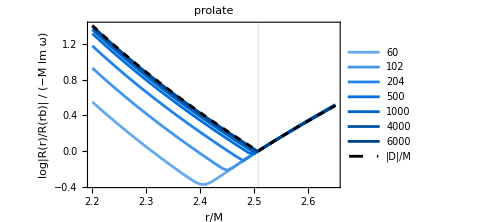
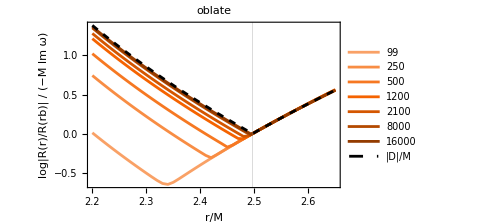

```mathematica
radialPanel[family_] := ListLinePlot[
  Append[radialCurve[family, #] & /@ profilePoles[family], radialWKB[family]],
  PlotStyle -> profileStyle[family], PlotRange -> {{2.2, 2.65}, All},
  GridLines -> {{bounce[family]}, None}, PlotLabel -> family,
  PlotLegends -> Append[profilePoles[family], "|D|/M"],
  FrameLabel -> {"r/M", "log|R(r)/R(rb)| / (−M Im ω)"}];
Row[{radialPanel["prolate"], radialPanel["oblate"]}]
```

Colours label the overtones; dashed curves show |D|/M. The grey line marks the bounce.

## Angular projector (Fig. 3)

With the source on the equator, the projector is Π_n(θ,π/2)==S_n(θ)S_n(π/2)/N_n. Its logarithmic modulus divided by damping has the WKB limit [Eq. (33)]

(log|Π_n(θ,π/2)|)/(-ω_(I,n))⟶{ -a(1-sinθ),  |  pr, 
 0,  |  ob.

We add the equatorial value to log |(S_n(θ))/(√N_n)|. The coarse grid is θ_j=(j π)/60, with the equator at j=30.

```mathematica
projectorCurve[rec_] := With[{logS = rec["angular"][[All, 1]]},
  Table[{j/60, (logS[[j]] + logS[[30]])/rec["x"]}, {j, 6, 54}]];
(* The last angular entry of each map is the source at theta = Pi/2. *)
projectorCurve[family_, n_] := If[MemberQ[mapPairs[family], n],
  With[{rec = profileMap[family, n]},
    Transpose[{Most[rec["angles"]]/Pi, (Most[rec["ln_S"]] + Last[rec["ln_S"]])/rec["x"]}]],
  projectorCurve[record[family, n]]];
projectorWKB["prolate", theta_] := -2 a (1 - Sin[theta]);     (* a/M = 2a *)
projectorWKB["oblate", theta_] := 0;
```

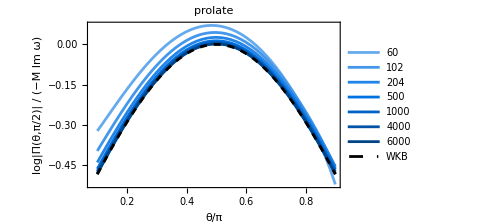
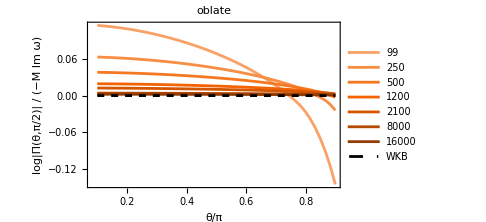

```mathematica
angularPanel[family_] := ListLinePlot[
  Append[projectorCurve[family, #] & /@ profilePoles[family],
    Table[{t, projectorWKB[family, Pi t]}, {t, 0.1, 0.9, 0.004}]],
  PlotStyle -> profileStyle[family], PlotRange -> All, PlotLabel -> family,
  PlotLegends -> Append[profilePoles[family], "WKB"],
  FrameLabel -> {"θ/π", "log|Π(θ,π/2)| / (−M Im ω)"}];
Row[{angularPanel["prolate"], angularPanel["oblate"]}]
```

Prolate profiles approach the angular WKB rate; oblate profiles approach zero. The latter limit is nonuniform near the south pole.

## 07 Growth-rate maps

The numerical rate is the secant of the complete residue logarithm. We compare it directly with the WKB rate.

log ℛ_n==log c_n+log f_n(r)+log f_n(r')+log(S_n(θ))/(√N_n)+log(S_n(θ'))/(√N_n)

Γ_ik^num==(log|ℛ_k|-log|ℛ_i|)/(ω_(I,i)-ω_(I,k)),    ω_(I,k)<ω_(I,i)

Γ_pr  |  ==|D_pr(r)|+|D_pr(r')|-a(2-sinθ-sin θ') 
 Γ_ob  |  ==|D_ob(r)|+|D_ob(r')|

Residues and optical rates

```mathematica
damping[rec_] := rec["x"];               (* x_n = -M omega_I *)
frequency[rec_] := N[rec["omega"]/2];    (* M omega *)
(* require a saved grid point rather than silently interpolate *)
gridIndex[grid_, value_] := With[{i = First[Nearest[N[grid] -> "Index", value]]},
   If[Abs[N[grid[[i]]] - value] < 10^-9, i, Missing["OffGrid", value]]];
radialAt[rec_, r_] := rec["radial"][[gridIndex[2 radii, r]]];      (* radii is in units 2M = 1 *)
angularAt[rec_, theta_] := rec["angular"][[gridIndex[angles, theta]]];
(* {log|R_n|, phase sum} at {r/M, r'/M, theta, theta'} *)
logResidue[rec_, {r_, rPrime_, theta_, thetaPrime_}] := rec["constant"] +
   radialAt[rec, r] + radialAt[rec, rPrime] + angularAt[rec, theta] + angularAt[rec, thetaPrime];
spin = 2 a;    (* a/M = 7/10 *)
(* position = {r/M, r'/M, theta, theta'} *)
gammaWKB["prolate", {r_, rPrime_, theta_, thetaPrime_}] :=
  Abs[opticalDistance["prolate", r]] + Abs[opticalDistance["prolate", rPrime]] -
   spin (2 - Sin[theta] - Sin[thetaPrime]);
gammaWKB["oblate", {r_, rPrime_, theta_, thetaPrime_}] :=
  Abs[opticalDistance["oblate", r]] + Abs[opticalDistance["oblate", rPrime]];
(* the two radial actions contribute 2 i beta_sigma *)
opticalTime["prolate", {r_, rPrime_, theta_, thetaPrime_}] :=
   opticalDistance["prolate", r] + opticalDistance["prolate", rPrime] +
   2 I imaginaryAction["prolate"] - spin (2 - Sin[theta] - Sin[thetaPrime]);
opticalTime["oblate", {r_, rPrime_, theta_, thetaPrime_}] :=
   opticalDistance["oblate", r] + opticalDistance["oblate", rPrime] +
   2 I imaginaryAction["oblate"] + I spin (2 - Cos[theta] - Cos[thetaPrime]);
```

The source is (3M, π/2). We use oblate 8000/16000 and prolate 4000/6000. The radial mesh spans 2.2M–3.2M and has spacing 0.0002M near each bounce; there are 577 angles between π/10 and 9π/10. A new calculation also includes the bounce itself.

Combine the radial and angular factors

```mathematica
(* Cell 1: growth rates. The JSON files contain both source factors at the end.
   The radial grids differ between families; angles are common. *)
mapPair = <|"oblate" -> {8000, 16000}, "prolate" -> {4000, 6000}|>;
mapFamilies = Keys[mapPair];
Clear[mapData];
mapData[family_] := mapData[family] = Table[
  Association[readData[FileNameJoin[{dataDirectory, "maps", family <> "_" <> ToString[n] <> ".json"}]]],
  {n, mapPair[family]}];
mapRealQ[z_] := NumberQ[z] && TrueQ[Im[z] == 0];
mapAngles = Most[First[mapData[First[mapFamilies]]]["angles"]];

Do[Module[{records = mapData[family], first, second, x, valid, logR},
  {first, second} = records;
  mapRadii[family] = Drop[first["radii"], -2];
  x = Lookup[records, "x"];
  valid = And[
    VectorQ[x, mapRealQ], TrueQ[0 < First[x] < Last[x]],
    first["radii"] === second["radii"], first["angles"] === second["angles"],
    Most[first["angles"]] === mapAngles,
    VectorQ[mapRadii[family], mapRealQ], VectorQ[mapAngles, mapRealQ],
    And @@ Thread[Differences[mapRadii[family]] > 0], And @@ Thread[Differences[mapAngles] > 0],
    TrueQ[Abs[Last[first["radii"]] - 3] < 10^-12],
    TrueQ[Abs[Last[first["angles"]] - Pi/2] < 10^-12],
    And @@ Flatten[Table[And[
      rec["family"] === family, rec["n"] === mapPair[family][[j]],
      mapRealQ[rec["ln_abs_c"]], VectorQ[rec["ln_f"], mapRealQ], VectorQ[rec["ln_S"], mapRealQ],
      Length[rec["ln_f"]] == Length[rec["radii"]],
      Length[rec["ln_S"]] == Length[rec["angles"]]],
      {j, 2}, {rec, {records[[j]]}}]]];
  If[! TrueQ[valid], Print["Check the map data for ", family, "."]; Abort[]];
  (* log|c f(r) f(3M) S(theta)/sqrt(N) S(pi/2)/sqrt(N)| *)
  logR[rec_] := rec["ln_abs_c"] + Last[rec["ln_f"]] + Last[rec["ln_S"]] +
    Outer[Plus, Most[rec["ln_S"]], Drop[rec["ln_f"], -2]];
  mapSecant[family] = (logR[second] - logR[first])/(Last[x] - First[x]);
  mapWKB[family] = Table[gammaWKB[family, {r, 3, theta, Pi/2}],
    {theta, mapAngles}, {r, mapRadii[family]}];
  If[! MatrixQ[mapWKB[family], mapRealQ] || ! TrueQ[Min[mapWKB[family]] > 0] ||
      ! MatrixQ[mapSecant[family], mapRealQ], Print["Check the growth rates for ", family, "."]; Abort[]];
  mapPercent[family] = 100 (mapSecant[family] - mapWKB[family])/mapWKB[family];
], {family, mapFamilies}];
```

```mathematica
(* Cell 2: the paper's six panels, on the full spatial grid. *)
rateRange = MinMax[mapWKB /@ mapFamilies];
rateLevels = Range[Ceiling[First[rateRange], 0.2], Last[rateRange], 0.2];
rateColor[g_] := ColorData["BlueGreenYellow"][Rescale[g, rateRange]];
percentColor[e_] := ColorData["ThermometerColors"][Rescale[e, {-1, 1}]];
mapRange = {{2.2, 3.2}, MinMax[mapAngles]/Pi};
(* Explicit coordinates retain the finer radial spacing near the bounce. *)
mapTriples[family_, matrix_, step_:1] := Flatten[Table[
  {mapRadii[family][[j]], mapAngles[[i]]/Pi, matrix[[i, j]]},
  {i, 1, Length[mapAngles], step}, {j, Length[mapRadii[family]]}], 1];
rateLines[family_, matrix_] := ListContourPlot[mapTriples[family, matrix, 8],
  Contours -> rateLevels, ContourShading -> None, ContourStyle -> White];
mapPanel[family_, matrix_, color_, label_, lines_] := Show[
  ListDensityPlot[mapTriples[family, matrix], InterpolationOrder -> 1, MaxPlotPoints -> Infinity,
    ColorFunctionScaling -> False, ColorFunction -> color, PlotRangePadding -> None],
  lines, Graphics[{Dashed, Line[{{bounce[family], 0.1}, {bounce[family], 0.9}}]}],
  Frame -> True, FrameLabel -> {"r/M", "θ/π"}, PlotLabel -> label,
  PlotRange -> mapRange, AspectRatio -> 0.8, ImageSize -> 240,
  LabelStyle -> {FontFamily -> "Times", FontSize -> 11}];
gammaSymbol[family_] := Subscript["Γ", sigmaName[family]];
secantSymbol = Subsuperscript["Γ", "ik", "num"];
mapRow[family_] := {
  mapPanel[family, mapWKB[family], rateColor, Row[{gammaSymbol[family], "/M"}],
    rateLines[family, mapWKB[family]]],
  mapPanel[family, mapSecant[family], rateColor, Row[{secantSymbol, "/M"}],
    rateLines[family, mapSecant[family]]],
  mapPanel[family, mapPercent[family], percentColor,
    Row[{"100 (", secantSymbol, " − ", gammaSymbol[family], ")/", gammaSymbol[family]}],
    Graphics[]]};
mapPreview = Grid[{mapRow["oblate"], mapRow["prolate"],
  {BarLegend[{"BlueGreenYellow", rateRange}, LegendLabel -> "Γ/M", LegendLayout -> "Row"],
   SpanFromLeft,
   BarLegend[{"ThermometerColors", {-1, 1}}, LegendLabel -> "percent", LegendLayout -> "Row"]}}];
mapPreview
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
 |  |

```mathematica
(* Cell 3: maxima over every saved point, including the fine strip below the bounce. *)
mapSummaryRows = Table[With[{error = Abs[mapPercent[f]]},
  With[{at = First[Position[error, Max[error]]]},
    {f, Row[mapPair[f], "/"], Max[error], mapRadii[f][[at[[2]]]], mapAngles[[at[[1]]]]/Pi}]],
  {f, mapFamilies}];
mapSummary = Grid[Prepend[Table[
  {row[[1]], row[[2]], NumberForm[row[[3]], {5, 3}], NumberForm[row[[4]], {6, 4}], row[[5]]},
  {row, mapSummaryRows}],
  {"family", "poles", "max |difference| (%)", "r/M", "θ/π"}], Frame -> All];
mapSummary
```

family | poles | max |difference| (%) | r/M | θ/π
oblate | //800016000 | 0.911 | 2.4946 | 0.1
prolate | //40006000 | 0.653 | 2.5060 | 0.1

The panels show the WKB rate, the numerical rate and their percentage difference over the full grid. These percentages compare finite-overtone rates with WKB; they are not solver errors.

```mathematica
mapTargetMet = And @@ Table[Max[Abs[mapPercent[f]]] < 1, {f, mapFamilies}];
If[!mapTargetMet, Print["The new map exceeds 1%; inspect the displayed maximum before using it."]];
```

Full-resolution table

```mathematica
(* Optional export input: one row per point, without rounding or resampling. *)
mapExportRows[family_] := Prepend[Flatten[Table[
  {mapRadii[family][[j]], mapAngles[[i]], mapSecant[family][[i, j]],
   mapWKB[family][[i, j]], mapPercent[family][[i, j]]},
  {i, Length[mapAngles]}, {j, Length[mapRadii[family]]}], 1],
  {"r_over_M", "theta", "gamma_num_over_M", "gamma_WKB_over_M", "difference_percent"}];
```

## 08 Damping powers and complex ratios

At the equator we remove the WKB exponential and fit the remaining damping power, including the 1/x term.

log|ℛ_(σ,n)|+Γ_σ ω_(I,n)≃c+p_σ log(-M ω_(I,n))+b/(-M ω_(I,n))

The source radius is 2.6M; the observer is at 2.8M for prolate and 3.2M for oblate. The fits use x ≥ 100 and x ≥ 240, including the four higher poles used for the maps.

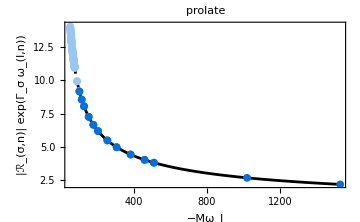
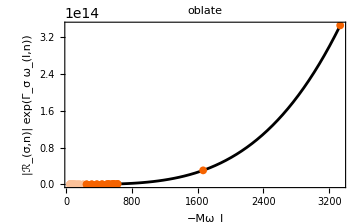

```mathematica
fitPosition = <|"prolate" -> {2.8, 2.6, Pi/2, Pi/2}, "oblate" -> {3.2, 2.6, Pi/2, Pi/2}|>;
reducedLog[rec_] := With[{family = rec["family"]},
   First[logResidue[rec, fitPosition[family]]] - gammaWKB[family, fitPosition[family]] damping[rec]];
(* The four high modes already contain the radial and equatorial factors. *)
highReducedLog[rec_] := Module[{family = rec["family"], fAt},
   fAt[r_] := rec["ln_f"][[First[FirstPosition[rec["radii"], q_ /; Abs[q - r] < 10^-12]]]];
   rec["ln_abs_c"] + Total[fAt /@ Take[fitPosition[family], 2]] + 2 Last[rec["ln_S"]] -
    gammaWKB[family, fitPosition[family]] rec["x"]];
(* {n, damping, reduced logarithm}; display x >= 50 and keep the same fit thresholds. *)
powerData = Association[Table[family -> SortBy[Join[
      Table[{rec["n"], damping[rec], reducedLog[rec]},
       {rec, Select[records[family], damping[#] >= 50 &]}],
      Table[{rec["n"], rec["x"], highReducedLog[rec]}, {rec, mapData[family]}]], First],
    {family, {"prolate", "oblate"}}]];
fitStart = <|"prolate" -> 100, "oblate" -> 240|>;
powerFit = Association[Table[family -> Module[{x},
      LinearModelFit[Select[powerData[family], #[[2]] >= fitStart[family] &][[All, {2, 3}]],
       {Log[x], 1/x}, x]], {family, {"prolate", "oblate"}}]];
powerPoints = Flatten[Table[
    {family, row[[1]], row[[2]], Exp[row[[3]]], row[[2]] >= fitStart[family]},
    {family, {"prolate", "oblate"}}, {row, powerData[family]}], 1];
powerPanel[family_] := Module[{fit = powerFit[family], start = fitStart[family], inFit, below},
   inFit = Cases[powerPoints, {family, _, x_, y_, True} :> {x, y}];
   below = Cases[powerPoints, {family, _, x_, y_, False} :> {x, y}];
   Show[Plot[Exp[fit[x]], {x, start, Max[First /@ inFit]}, PlotStyle -> Black],
    Plot[Exp[fit[x]], {x, 50, start}, PlotStyle -> Directive[Black, Dashed]],
    ListPlot[{below, inFit}, PlotStyle -> {Lighter[familyColor[family], 0.6], familyColor[family]},
     PlotMarkers -> {"●", 8}],
    PlotRange -> {{0, 1.05 Max[First /@ inFit]}, {0, All}}, PlotLabel -> family,
    FrameLabel -> {Row[{"−M", Subscript["ω", "I"]}],
      Row[{"|", Subscript["ℛ", "σ,n"], "| exp(", Subscript["Γ", "σ"],
        " ", Subscript["ω", "I,n"], ")"}]}]];
Row[{powerPanel["prolate"], powerPanel["oblate"]}]
```

```mathematica
Table[{family, powerFit[family]["BestFitParameters"][[2]]},
  {family, {"prolate", "oblate"}}] // TableForm
```

prolate | -0.500577
oblate | 3.49993

Points are the numerical residues; lines are the fits. The fitted powers approach −1/2 and 7/2.

t_pr  |  ==z_pr(r)+z_pr(r')-a(2-sinθ-sin θ') 
 t_ob  |  ==z_ob(r)+z_ob(r')+ia(2-cosθ-cos θ')

These complex optical times apply when both radial points are outside the bounce, with z = D + iβ. They fix the phase of the ratio as well as its modulus.

P_ik^num  |  ==ℛ_k/ℛ_i, 
 P_ik^WKB  |  ==((-ω_(I,k))/(-ω_(I,i)))^p_σ e^(i(ω_k-ω_i)t_σ)

For the ratios we use prolate 1000/1001 and oblate 2100/2101, with source (2.6M, π/2) and observer radius 2.8M.

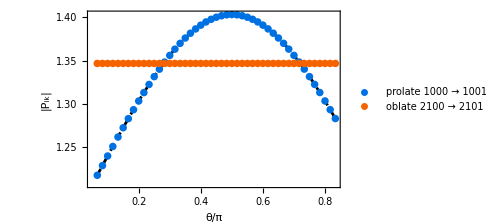
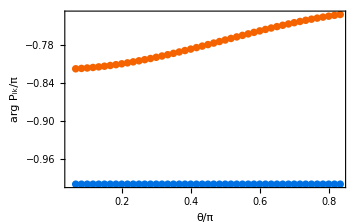

```mathematica
(* return {log|P_ik|, arg P_ik} *)
ratio[{i_, k_}, position_] := Module[{logModulus, phase},
   {logModulus, phase} = logResidue[k, position] - logResidue[i, position];
   {logModulus, Mod[phase, 2 Pi, -2 Pi]}];    (* in [-2 Pi, 0): phases near -Pi stay on one branch *)
candidate = <|"oblate" -> 7/2, "prolate" -> -1/2|>;
ratioWKB[{i_, k_}, position_] :=
  With[{exponent = I (frequency[k] - frequency[i]) opticalTime[i["family"], position]},
   {candidate[i["family"]] Log[damping[k]/damping[i]] + Re[exponent],
    Mod[Im[exponent], 2 Pi, -2 Pi]}];
scanPairs = <|"prolate" -> {1000, 1001}, "oblate" -> {2100, 2101}|>;
(* observer at (2.8 M, j Pi/60), source at (2.6 M, Pi/2);
   one row per angle: {theta/Pi, |P|, arg P/Pi, |P^WKB|, arg P^WKB/Pi} *)
ratioScan[family_] := Module[{pair = record[family, #] & /@ scanPairs[family],
    position, logP, argP, logWKB, argWKB},
   Table[position = {2.8, 2.6, j Pi/60, Pi/2};
    {logP, argP} = ratio[pair, position];
    {logWKB, argWKB} = ratioWKB[pair, position];
    {j/60, Exp[logP], argP/Pi, Exp[logWKB], argWKB/Pi}, {j, 4, 50}]];
ratioData = AssociationMap[ratioScan, {"prolate", "oblate"}];
(* column 2 of ratioData is the modulus, column 3 the phase; the WKB value comes two columns later *)
ratioPanel[column_, label_] := ListPlot[
   {ratioData["prolate"][[All, {1, column + 2}]], ratioData["oblate"][[All, {1, column + 2}]],
    ratioData["prolate"][[All, {1, column}]], ratioData["oblate"][[All, {1, column}]]},
   Joined -> {True, True, False, False},
   PlotStyle -> {Directive[Black, Dashed], Directive[Black, Dashed],
     Directive[PointSize[0.015], familyColor["prolate"]], Directive[PointSize[0.015], familyColor["oblate"]]},
   PlotRange -> All, FrameLabel -> {"θ/π", label}];
Legended[Row[{ratioPanel[2, Row[{"|", Subscript["P", "ik"], "|"}]],
   ratioPanel[3, Row[{"arg ", Subscript["P", "ik"], "/π"}]]}],
 PointLegend[{familyColor["prolate"], familyColor["oblate"]},
  {"prolate 1000 → 1001", "oblate 2100 → 2101"}]]
```

Points are numerical ratios; dashed curves use the WKB prediction. No phase offset is fitted.

## 09 Analytic geometry

These figures evaluate the paper's analytic formulas.

```mathematica
(* M = 1 here; chi is the dimensionless spin *)
deltaAt[chi_, r_] := r^2 - 2 r + chi^2;
q0At[chi_, r_] := (r^2 + chi^2)^2 - chi^2 deltaAt[chi, r];
tortoiseAt[chi_, r_] := With[{rp = 1 + Sqrt[1 - chi^2], rm = 1 - Sqrt[1 - chi^2]},
   r + (2 rp Log[(r - rp)/2] - 2 rm Log[(r - rm)/2])/(rp - rm)];
```

The oblate bounce solves r_*(r_b^ob)==Re r_*(ia); its radius is independent of the logarithm branches. The prolate action starts at the first-quadrant root r_tp of q_0==r(r^3+a^2 r+2 a^2).

For the prolate action the contour passes above the horizons; the square-root branch is positive on the real exterior.

lim_(r→∞) (Γ_ob-Γ_pr)==2∫_(r_b^ob)^(r_b^pr) (u^2+a^2)/Δ du+∫_(r_b^pr)^∞ (a^2 du)/(u^2+a^2+√(q_0(u)))

Bounce radii and the large-radius rate difference

```mathematica
(* both roots remain near 2.5 M *)
bounceAt["oblate", chi_] := Module[{r},
   r /. FindRoot[tortoiseAt[chi, r] == Re[tortoiseAt[chi, I chi]], {r, 2.5}, AccuracyGoal -> 13,
       PrecisionGoal -> 13]];
bounceAt["prolate", chi_] := Module[{z, r, tp, zMinus, slope, atThree, action},
   tp = SelectFirst[z /. NSolve[z^3 + chi^2 z + 2 chi^2 == 0, z], Im[#] > 0 &];
   zMinus = -2 Re[tp];    (* the three roots add up to zero *)
   slope[z_] := Sqrt[z] Sqrt[z - zMinus] Sqrt[z - tp] Sqrt[z - Conjugate[tp]]/deltaAt[chi, z];
   atThree = Re[NIntegrate[slope[z], {z, tp, 3 + I, 3}, PrecisionGoal -> 13]];
   action[r_?NumericQ] := atThree + NIntegrate[Sqrt[q0At[chi, u]]/deltaAt[chi, u], {u, 3, r},
       PrecisionGoal -> 13];
   r /. FindRoot[action[r], {r, 2.5}, AccuracyGoal -> 13, PrecisionGoal -> 13]];
(* the absolute goal also handles the zero Schwarzschild gap *)
asymptoticGap[{chi_, outer_, inner_}] :=
  2 NIntegrate[(u^2 + chi^2)/deltaAt[chi, u], {u, inner, outer},
      PrecisionGoal -> 13, AccuracyGoal -> 15] +
   NIntegrate[chi^2/(u^2 + chi^2 + Sqrt[q0At[chi, u]]), {u, outer, Infinity},
      PrecisionGoal -> 13, AccuracyGoal -> 15];
(* sample more densely near zero and extremal spin *)
spins = Join[0.002 25^(Range[0, 11]/11), Subdivide[0.06, 0.94, 66],
   1 - 0.05 (1/50)^(Range[0, 11]/11)];
schwarzschildBounce = 2 (1 + ProductLog[1/E]);
bounceRows = N[Join[{{0, schwarzschildBounce, schwarzschildBounce}},
    Table[{chi, bounceAt["prolate", chi], bounceAt["oblate", chi]}, {chi, spins}],
    {{1, 1 + Sqrt[2], 1 + Sqrt[2]}}]];
gaps = asymptoticGap /@ bounceRows;
```

## Bounce radii (Fig. 1)

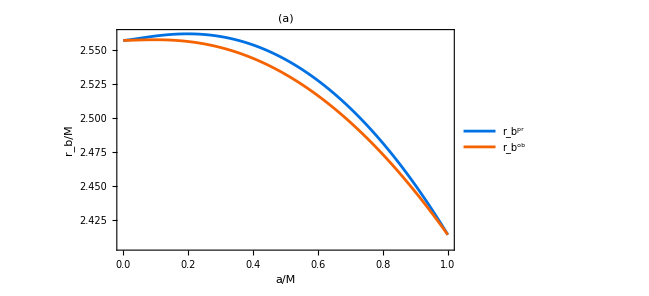
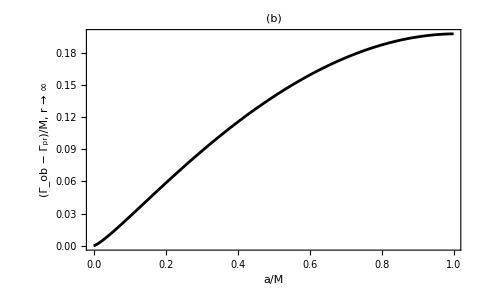

```mathematica
figure1 = Column[{
  ListLinePlot[{bounceRows[[All, {1, 2}]], bounceRows[[All, {1, 3}]]},
   PlotStyle -> {familyColor["prolate"], familyColor["oblate"]},
   PlotLegends -> {Subsuperscript["r", "b", "pr"], Subsuperscript["r", "b", "ob"]},
   FrameLabel -> {"a/M", Row[{Subscript["r", "b"], "/M"}]},
   PlotLabel -> "(a)", ImageSize -> 480],
  ListLinePlot[Transpose[{bounceRows[[All, 1]], gaps}], PlotStyle -> Black,
   FrameLabel -> {"a/M", Row[{"(", Subscript["Γ", "ob"], " − ", Subscript["Γ", "pr"], ")/M,  r → ∞"}]},
   PlotLabel -> "(b)", ImageSize -> 480]}, Alignment -> Center];
figure1
```

Bounce radii and the asymptotic difference between the two rates.

Γ_ob-Γ_pr==J(r)+J(r')+a(2-sinθ-sin θ')

J(r)=={ J_1-δ r_*(r),  |  r_+<r≤r_b^ob 
 2 r_*(r)-δ r_*(r)-J_2,  |  r_b^ob<r<r_b^pr 
 δ r_*(r)-J_1,  |  r≥r_b^pr

δ r_*(r)==∫_(r_+)^r (a^2 du)/(u^2+a^2+√(q_0(u)))

Optical-distance difference

```mathematica
{bob, bpr} = {bounce["oblate"], bounce["prolate"]};    (* a/M = 0.7 from here on *)
horizonRadius = N[2 rPlus];                            (* r_+/M *)
(* integrate the regular difference of the two optical slopes *)
rStarCorrection = Module[{y, r},
   NDSolveValue[{y'[r] == spin^2/(r^2 + spin^2 + Sqrt[q0At[spin, r]]), y[horizonRadius] == 0}, y,
    {r, horizonRadius, 12}, PrecisionGoal -> 14, AccuracyGoal -> 14, InterpolationOrder -> All]];
J1 = tortoiseAt[spin, bob] - tortoiseAt[spin, bpr] + rStarCorrection[bpr];
J2 = tortoiseAt[spin, bob] + tortoiseAt[spin, bpr] - rStarCorrection[bpr];
J[r_] := Which[r <= bob, J1 - rStarCorrection[r],
   r < bpr, 2 tortoiseAt[spin, r] - rStarCorrection[r] - J2,
   True, rStarCorrection[r] - J1];
Jbob = J[bob];
(* the dashed curve: source at the oblate bounce, both points on the equator *)
rateDifference[r_] := J[r] + Jbob;
(* include both kinks explicitly, with finer grids for the zooms *)
wideRadii = Union[Subdivide[horizonRadius, 12, 499], Subdivide[2.48, 2.52, 399], {bob, bpr}];
horizonRadii = Subdivide[horizonRadius, horizonRadius + 0.02, 199];
bounceRadii = Union[Subdivide[bob - 0.004, bpr + 0.004, 299], {bob, bpr}];
onRadii[f_, radii_] := Table[{r, f[r]}, {r, radii}];
```

## Optical-distance difference (Fig. 4)

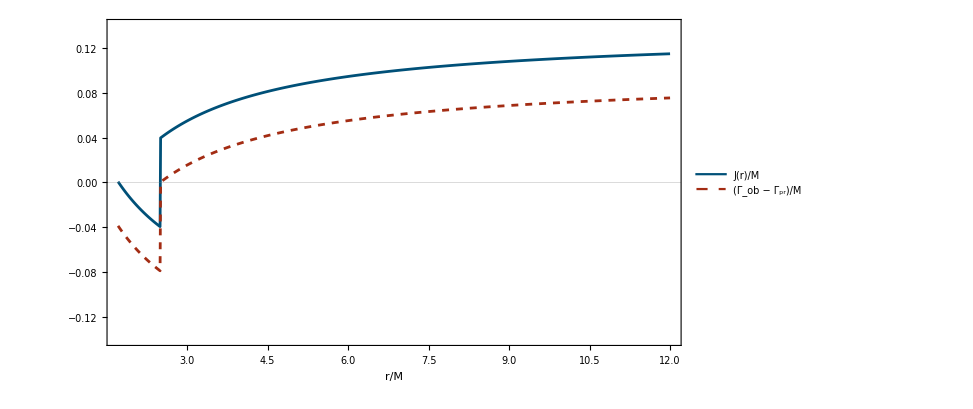

```mathematica
jStyles = {RGBColor["#005078"], Directive[RGBColor["#A32C13"], Dashed]};
jHorizon = ListLinePlot[onRadii[J, horizonRadii], PlotStyle -> First[jStyles],
   PlotRange -> {{horizonRadius, horizonRadius + 0.02}, {-0.00075, 0.0015}},
   GridLines -> {None, {0}}, FrameLabel -> {"r/M", None},
   FrameTicks -> {{{-0.0006, 0, 0.0006}, None},
     {{{horizonRadius, Subscript["r", "+"]}, {horizonRadius + 0.02, Row[{Subscript["r", "+"], "+0.02"}]}}, None}},
   BaseStyle -> {FontFamily -> "Times", FontSize -> 10}, Background -> White,
   ImagePadding -> {{55, 35}, {35, 8}}, ImageSize -> 245];
jBounces = ListLinePlot[{onRadii[J, bounceRadii], onRadii[rateDifference, bounceRadii]},
   PlotStyle -> jStyles, PlotRange -> {{bob - 0.004, bpr + 0.004}, {-0.092, 0.047}},
   GridLines -> {{bob, bpr}, {0}}, GridLinesStyle -> Directive[Gray, Dotted],
   FrameLabel -> {"r/M", None},
   FrameTicks -> {{{-0.08, 0, 0.04}, None},
     {{{bob, Subsuperscript["r", "b", "ob"]}, {bpr, Subsuperscript["r", "b", "pr"]}}, None}},
   BaseStyle -> {FontFamily -> "Times", FontSize -> 10}, Background -> White,
   ImagePadding -> {{40, 20}, {35, 8}}, ImageSize -> 245];
figure4 = Legended[
  ListLinePlot[{onRadii[J, wideRadii], onRadii[rateDifference, wideRadii]},
   PlotStyle -> jStyles, PlotRange -> {{horizonRadius, 12}, {-0.14, 0.14}},
   GridLines -> {None, {0}}, FrameLabel -> {"r/M", None},
   Epilog -> {Inset[jHorizon, Scaled[{0.35, 0.28}], Center, Scaled[{0.36, 0.42}]],
     Inset[jBounces, Scaled[{0.78, 0.28}], Center, Scaled[{0.36, 0.42}]]},
   AspectRatio -> 0.57, ImageSize -> 720],
  Placed[LineLegend[jStyles, {"J(r)/M", Row[{"(", Subscript["Γ", "ob"], " − ", Subscript["Γ", "pr"], ")/M"}]}, LegendLayout -> "Row", LabelStyle -> {FontFamily -> "Times", FontSize -> 13}], Above]];
figure4
```

The insets resolve the horizon and the two bounces.

max(r,r')≥r_b^pr ⟹ Γ_ob>Γ_pr,    Γ_pr>Γ_ob ⟺ sinθ+sin θ'>2+(J(r)+J(r'))/a

## Dominance regions (Fig. 5)

```mathematica
(* Blue: oblate larger; orange: prolate larger, as in the paper. *)
dominanceColors = {RGBColor["#E0A85C"], RGBColor["#4876A0"]};
dominanceMap[difference_, {xMin_, xMax_}, {yMin_, yMax_}, labels_, options___] :=
  ContourPlot[difference[x, y], {x, xMin, xMax}, {y, yMin, yMax}, Contours -> {0},
   ContourShading -> dominanceColors, ContourStyle -> Directive[RGBColor["#1F2A38"], Thick],
   PlotPoints -> 50, MaxRecursion -> 3, Exclusions -> None,
   FrameLabel -> labels, ImageSize -> 285, AspectRatio -> 1,
   PlotRangePadding -> None, options];
angleTicks = {0, Pi/2, Pi};
figure5 = Legended[GraphicsRow[{
  dominanceMap[Function[{theta, thetaPrime}, 2 Jbob + spin (2 - Sin[theta] - Sin[thetaPrime])],
   {0, Pi}, {0, Pi}, {"θ", "θ′"},
   FrameTicks -> {{angleTicks, None}, {angleTicks, None}}, PlotLabel -> "(a)"],
  dominanceMap[Function[{r, rPrime}, J[r] + J[rPrime]], {2.47, 2.52}, {2.47, 2.52},
   {"r/M", "r′/M"}, GridLines -> {{bob, bpr}, {bob, bpr}}, PlotLabel -> "(b)"],
  dominanceMap[Function[{r, theta}, J[r] + Jbob + spin (1 - Sin[theta])],
   {horizonRadius + 10^-4, 2.75}, {0, Pi}, {"r/M", "θ"},
   FrameTicks -> {{angleTicks, None}, {Automatic, None}}, PlotLabel -> "(c)"]}, ImageSize -> 900, Spacings -> 10],
  Placed[SwatchLegend[Reverse[dominanceColors],
    {Row[{Subscript["Γ", "ob"], " > ", Subscript["Γ", "pr"]}],
     Row[{Subscript["Γ", "pr"], " > ", Subscript["Γ", "ob"]}]}, LegendLayout -> "Row", LabelStyle -> {FontFamily -> "Times", FontSize -> 13}], Below]];
figure5
```

-Graphics-

Blue marks the larger oblate rate; orange marks the larger prolate rate.

τ_pr==t ⟺ D_pr(r)==±[t+a(1-sinθ)]

dr/dD==Δ/(√q_0),    r(0)==r_b^pr

Inverse optical distance and front radii

```mathematica
(* |D| <= 0.8 M + a on every profile, so D in [-1.5, 1.5] M is enough *)
radiusAtDistance[chi_, rb_] := Module[{x, d},
   NDSolveValue[{x'[d] == deltaAt[chi, x[d]]/Sqrt[q0At[chi, x[d]]], x[0] == rb}, x,
    {d, -1.5, 1.5}, PrecisionGoal -> 12, AccuracyGoal -> 12, InterpolationOrder -> All]];
schwarzschildRadius = radiusAtDistance[0, N[schwarzschildBounce]];
prolateRadius = radiusAtDistance[spin, bpr];
(* the profile at time t: D_pr(r) = side (t + a (1 - sin theta)),
   with side = +1 above the bounce and -1 below *)
frontRadius[radius_, chi_, side_, t_, theta_] := radius[side (t + chi (1 - Sin[theta]))];
(* the two arrow angles are grid points too *)
frontAngles = N[Union[Subdivide[0, Pi, 400], {Pi/6, Pi/3}]];
```

## Source and observer profiles (Fig. 6)

```mathematica
(* The source at t/M = -0.4 uses the positive time magnitude 0.4 in frontRadius. *)
frontStyles = {Directive[RGBColor["#A04B2D"], Dashed], Black,
   Directive[RGBColor["#1D6580"], Dashed]};
frontPanel[radius_, chi_, side_, title_] := Module[{at, profile, northTicks},
   at[t_, theta_] := frontRadius[radius, chi, side, t, theta];
   profile[t_] := Table[{at[t, theta], 1 - theta/Pi}, {theta, frontAngles}];
   northTicks = Table[{1 - t, t}, {t, {0, 1/6, 1/3, 1/2, 2/3, 5/6, 1}}];
   ListLinePlot[{profile[0.4], profile[0], profile[0.8]}, PlotStyle -> frontStyles,
    PlotRange -> {If[side < 0, {2.16, 2.60}, {2.48, 3.01}], {-0.03, 1.03}},
    FrameTicks -> {{northTicks, None}, {Automatic, None}},
    GridLines -> {If[chi == 0, None, {bpr}], {0, 1/2, 1}},
    GridLinesStyle -> Directive[LightGray, Dotted],
    Epilog -> {RGBColor["#A04B2D"], Arrowheads[0.025],
      Arrow[{{at[0.4, Pi/6], 5/6}, {at[0, Pi/6], 5/6}}],
      RGBColor["#1D6580"],
      Arrow[{{at[0, Pi/3], 2/3}, {at[0.8, Pi/3], 2/3}}]},
    FrameLabel -> {"r/M", "θ/π"}, PlotLabel -> title, AspectRatio -> 0.85, ImageSize -> 350]];
figure6 = Legended[Grid[{
  {frontPanel[schwarzschildRadius, 0, -1, "Schwarzschild, below"],
   frontPanel[schwarzschildRadius, 0, 1, "Schwarzschild, above"]},
  {frontPanel[prolateRadius, spin, -1, "Kerr prolate, below"],
   frontPanel[prolateRadius, spin, 1, "Kerr prolate, above"]}}],
  Placed[LineLegend[frontStyles, {"source: t/M = −0.4", "t = 0", "observer: t/M = +0.8"}, LegendLayout -> "Row", LabelStyle -> {FontFamily -> "Times", FontSize -> 13}], Above]];
figure6
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

Schwarzschild above, Kerr below; the source and observer lie below the bounce on the left and above it on the right.

## Files for the paper figures

New calculations are saved in data/. The tables/ folder contains the CSV files for the Python figures, including radial_profiles.csv and angular_projector.csv for all seven curves. Before the new run, import mode reads the completed data in output/.

Write the numerical and analytic tables

```mathematica
exportTables[records_, folder_] := Module[{rows = Flatten[Values[records]], write, radial, angular},
   write[name_, table_] := Export[FileNameJoin[{folder, name}], table /. _Missing -> "", "CSV"];
   write["poles.csv", Prepend[
     Table[{rec["family"], rec["n"], N[Re[rec["omega"]]/2], rec["x"],
        N[Re[rec["A"]]], N[Im[rec["A"]]], rec["constant"][[1]], rec["constant"][[2]],
        rec["iterations"], rec["lastMove"], rec["seedShift"], rec["seconds"], rec["converged"]},
       {rec, rows}],
     {"family", "n", "re_M_omega", "x", "re_A", "im_A", "ln_abs_c", "arg_c", "newton_steps",
      "last_step", "seed_shift", "seconds", "converged"}]];
   radial = Lookup[rows, "radial"];       (* per pole: {ln|f|, arg f} at each radius *)
   angular = Lookup[rows, "angular"];
   write["radial_ln_abs.csv", Prepend[radial[[All, All, 1]], N[2 radii]]];
   write["radial_arg.csv", Prepend[radial[[All, All, 2]], N[2 radii]]];
   write["angular_ln_abs.csv", Prepend[angular[[All, All, 1]], N[angles]]];
   write["angular_arg.csv", Prepend[angular[[All, All, 2]], N[angles]]];];
If[compute,
 tableFolder = FileNameJoin[{dataDirectory, "tables"}];
 If[!DirectoryQ[tableFolder], CreateDirectory[tableFolder]];
 writeTable[name_, header_, rows_] := Export[FileNameJoin[{tableFolder, name}], Prepend[rows, header], "CSV"];
 exportTables[records, tableFolder];
writeTable["radial_profiles.csv", {"family", "n", "r_over_M", "log_ratio_over_damping"},
  Flatten[Table[Join[{family, n}, row], {family, Keys[profilePoles]},
    {n, profilePoles[family]}, {row, radialCurve[family, n]}], 2]];
writeTable["angular_projector.csv", {"family", "n", "theta_over_pi", "log_projector_over_damping"},
  Flatten[Table[Join[{family, n}, row], {family, Keys[profilePoles]},
    {n, profilePoles[family]}, {row, projectorCurve[family, n]}], 2]];
writeTable["modulo_e_fase.csv",
  {"family", "theta_over_pi", "abs_P", "arg_P_over_pi", "abs_P_wkb", "arg_P_wkb_over_pi"},
  Flatten[Table[Prepend[N[row], family],
    {family, {"prolate", "oblate"}}, {row, ratioData[family]}], 1]];
writeTable["power_fits_linear.csv", {"family", "n", "damping", "reduced_magnitude", "in_fit"},
  powerPoints];
writeTable["power_fits_coefficients.csv", {"family", "c", "p", "b"},
  Table[Prepend[powerFit[family]["BestFitParameters"], family], {family, {"prolate", "oblate"}}]];
writeTable["geometry_bounce_spin.csv",
  {"a_over_M", "rb_pr_over_M", "rb_ob_over_M", "full_delta_Gamma_infinity_over_M"},
  Join[bounceRows, Transpose[{gaps}], 2]];
(* the grids of Figs. 4 and 5; as in the paper figure, panel c starts 1e-4 M above the horizon *)
jGrids = <|"wide" -> wideRadii, "horizon" -> horizonRadii, "bounces" -> bounceRadii,
   "dominance_b" -> Subdivide[2.47, 2.52, 499],
   "dominance_c" -> Subdivide[horizonRadius + 10^-4, 2.75, 499]|>;
writeTable["geometry_J.csv", {"grid", "r_over_M", "J_over_M", "Gamma_difference_over_M"},
  Flatten[Table[{name, r, J[r], rateDifference[r]}, {name, Keys[jGrids]}, {r, jGrids[name]}], 1]];
(* t_over_M stores time magnitudes: 0.4 is the source at -0.4M; 0.8 is the observer at +0.8M. *)
frontRows[radius_, chi_] := Flatten[Table[
    N[{chi, side, t, theta, frontRadius[radius, chi, side, t, theta]}],
    {side, {-1, 1}}, {t, {0.4, 0, 0.8}}, {theta, frontAngles}], 2];
writeTable["geometry_fronts.csv", {"a_over_M", "side", "t_over_M", "theta", "r_over_M"},
  Join[frontRows[schwarzschildRadius, 0], frontRows[prolateRadius, spin]]];
 Do[Export[FileNameJoin[{tableFolder, "growth_map_" <> family <> ".csv"}], mapExportRows[family], "CSV"], {family, mapFamilies}];
 Export[FileNameJoin[{tableFolder,"map_maxima.csv"}], Prepend[(List@@# & /@ mapSummaryRows) /. Row[x_,_] :> StringRiffle[ToString /@ x,"/"], {"family","poles","max_percent","r_over_M","theta_over_pi"}], "CSV"];
 CopyFile[FileNameJoin[{dataDirectory,"maps","fine_radial_ln_abs.csv"}],FileNameJoin[{tableFolder,"fine_radial_ln_abs.csv"}],OverwriteTarget->True];
 saveData[FileNameJoin[{dataDirectory,"complete.wxf"}], <|"finished" -> DateString[], "map_max_percent" -> (Max[Abs[mapPercent[#]]]& /@ mapFamilies), "below_one_percent" -> And@@(Max[Abs[mapPercent[#]]]<1& /@ mapFamilies)|>];
];
```

The supplied high-overtone maps have maximum WKB differences of 0.911% and 0.653% on the refined mesh. Increasing radial truncation and angular precision leaves their stored profiles unchanged at the displayed precision. The new run reports its own maxima above.